## Working with NumericArray

This example demonstrates working with NumericArrays. NumericArray support requires Mathematica 12.0 or later.

Note:  NumericArray replaces the earlier undocumented RawArray.

```mathematica
Needs["LTemplate`"]
SetDirectory@NotebookDirectory[];
```

```mathematica
template=
LClass["NA",
{
LFun["shuffle",{{LType[List,Real,1],"Constant"}},LType[NumericArray,"Byte"]],
LFun["deshuffle",{{LType[NumericArray,"Byte"],"Constant"}},LType[List,Real,1]],

LFun["safeConvertToBytes",{{NumericArray,"Constant"}},ByteArray],
LFun["convertToFloat",{{NumericArray,"Constant"},Integer,Real},LType[NumericArray,"Real32"]],
LFun["convertToInteger16",{{NumericArray,"Constant"},Integer,Real},LType[NumericArray,"Integer16"]]
}
];
```

```mathematica
CompileTemplate[template]
```

Current directory is: /Users/szhorvat/Repos/LTemplate/LTemplate/Documentation/Examples/NumericArray

Unloading library NA ...

Generating library code ...

Compiling library code ...

/Users/szhorvat/Library/Mathematica/SystemFiles/LibraryResources/MacOSX-x86-64/NA.dylib

```mathematica
LoadTemplate[template]
```

```mathematica
obj=Make[NA];
```

This table of real numbers takes up 800 kB of storage.

```mathematica
data=Table[Sin[x],{x,0,100,0.001}];
```

```mathematica
ByteCount[data]
```

800152

However, there is a lot of redundancy in the numbers as they represent a continuous function.

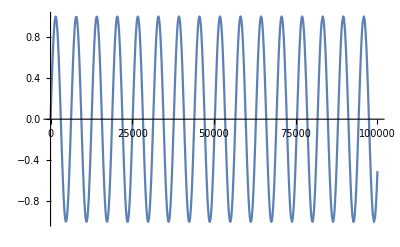

```mathematica
ListLinePlot[data,MaxPlotPoints->500]
```

It is reasonable to expect this data to compress well, but BinarySerialize (which also performs compression with the PerformanceGoal→"Size" option) does not do very well on it. The result is 750 kB, only a 6% reduction from the original size.

```mathematica
BinarySerialize[data,PerformanceGoal->"Size"]
```

ByteArray[…]

```mathematica
ByteCount[%]/ByteCount[data]//N
```

0.937906

The compressibility can be improved considerably by rearranging the underlying bytes of the data so that the first byte of each floating point number are stored contiguously, followed by the second bytes, and so on. This exposes the redundancy in the data. The shuffle function performs this rearranging.

```mathematica
obj@"shuffle"[data]
```

NumericArray[…]

```mathematica
BinarySerialize[obj@"shuffle"[data],PerformanceGoal->"Size"]
```

ByteArray[…]

Now we have a 31% reduction.

```mathematica
ByteCount[%]/ByteCount[data]//N
```

0.684997

The compressibility could be improved further (at the cost of some numerical accuracy) by storing only the differences between the consecutive numbers.  The following functions implement this:

```mathematica
compress[data_?(VectorQ[#,Developer`MachineRealQ]&)]:=
BinarySerialize[
obj@"shuffle"[Prepend[Differences[data],First[data]]],
PerformanceGoal->"Size"
]
```

```mathematica
decompress[bytes_]:=Accumulate[obj@"deshuffle"[BinaryDeserialize[bytes]]]
```

```mathematica
compress[data]
```

ByteArray[…]

This way we could achieve a 45% reduction in size.

```mathematica
ByteCount@compress[data]/ByteCount[data]//N
```

0.549854

For practical purposes, the accuracy loss is negligible.

```mathematica
Abs[decompress@compress[data]-data]//Max
```

1.73472×10^-18

### Converting between NumericArray types

The following function takes a NumericArray of arbitrary type, and converts it to a ByteArra provided that all elements are representable as an unsigned byte value.

```mathematica
obj@"safeConvertToBytes"[NumericArray[{1,2,3},"Integer64"]]
```

ByteArray[…]

```mathematica
obj@"safeConvertToBytes"[NumericArray[{1,2,3,-1},"Integer64"]]
```

LTemplate::error: MNumericArray_convertType() failed. Check that all values can be converted to the target type using the specified method and tolerance.

LibraryFunctionError[LIBRARY_FUNCTION_ERROR,6]

```mathematica
obj@"safeConvertToBytes"[NumericArray[{1.0,2.0,3.0},"Real64"]]
```

ByteArray[…]

```mathematica
obj@"safeConvertToBytes"[NumericArray[{1.0,2.5,3.0},"Real64"]]
```

LTemplate::error: MNumericArray_convertType() failed. Check that all values can be converted to the target type using the specified method and tolerance.

LibraryFunctionError[LIBRARY_FUNCTION_ERROR,6]

Set up conversion method mapping for subsequent example.

```mathematica
methods=AssociationThread[{"Check","ClipAndCheck","Coerce","ClipAndCoerce","Round","ClipAndRound","Scale","ClipAndScale"},Range[8]]
```

<|Check→1,ClipAndCheck→2,Coerce→3,ClipAndCoerce→4,Round→5,ClipAndRound→6,Scale→7,ClipAndScale→8|>

Conversion fails when precision would be lost.

```mathematica
obj@"convertToFloat"[NumericArray[{1,√2,3},"Real64"],methods["Check"],0]
```

LTemplate::error: MNumericArray_convertType() failed. Check that all values can be converted to the target type using the specified method and tolerance.

LibraryFunctionError[LIBRARY_FUNCTION_ERROR,6]

Let us use a tolerance of 10 decimal digits. Now the conversion succeeds.

```mathematica
obj@"convertToFloat"[NumericArray[{1,√2,3},"Real64"],methods["Check"],10]
```

NumericArray[…]

```mathematica
Normal[%]
```

{1.,1.41421,3.}

Coerce the 64-bit floating point value into a 32-bit one.

```mathematica
obj@"convertToFloat"[NumericArray[{1,√2,3},"Real64"],methods["Coerce"],0]//Normal
```

{1.,1.41421,3.}

The conversion fails if a value is outside of the target type range.

```mathematica
obj@"convertToFloat"[NumericArray[{1,2,10^50},"Real64"],methods["Check"],0]
```

LTemplate::error: MNumericArray_convertType() failed. Check that all values can be converted to the target type using the specified method and tolerance.

LibraryFunctionError[LIBRARY_FUNCTION_ERROR,6]

Clip the value to the range of the target type.

```mathematica
obj@"convertToFloat"[NumericArray[{1,2,10^50},"Real64"],methods["ClipAndCheck"],0]//Normal
```

{1.,2.,3.40282×10^38}

Clip to the target integer range.

```mathematica
obj@"convertToInteger16"[NumericArray[{1,2,100000},"Real64"],methods["ClipAndCheck"],0]//Normal
```

{1,2,32767}

Scale the source range into the target range. Floating point ranges are 0..1 or -1..1. Warning: As of Mathematica 12.0, the Scale methods are not yet documented.

```mathematica
obj@"convertToInteger16"[NumericArray[{-2500000,1,500000,10000000},"Integer32"],methods["Scale"],0]//Normal
```

{-39,0,7,152}

```mathematica
obj@"convertToInteger16"[NumericArray[{0,0.5,1},"Real64"],methods["Scale"],0]//Normal
```

{0,16383,32767}

### Working directly with ByteArrays

LibraryFunctionLoad does support ByteArray as a type specification. The corresponding type in C is an MNumericArray of rank 1 and element type "Byte".

LTemplate does correspondingly accept LType[ByteArray] or ByteArray as a type specification too, and treats ByteArrays as mma::NumericArrayRef<uint8_t> in C++. This allows passing and returning ByteArrays directly, without a need for explicit conversion.

The following example loads the same library using a different type annotation, so that results can be obtained directly as ByteArray.

```mathematica
UnloadTemplate[template]
```

```mathematica
template=
LClass["NA",
{
LFun["shuffle",{{LType[List,Real,1],"Constant"}},ByteArray],
LFun["deshuffle",{{ByteArray,"Constant"}},LType[List,Real,1]]
}
];
```

```mathematica
LoadTemplate[template]
```

```mathematica
obj=Make[NA];
```

```mathematica
obj@"shuffle"[data]
```

ByteArray[…]

```mathematica
BinarySerialize[#,PerformanceGoal->"Size"]&/@{data,obj@"shuffle"[data]}
```

{ByteArray[…],ByteArray[…]}

Deshuffle a shuffled ByteArray.

```mathematica
obj@"deshuffle"[obj@"shuffle"[{1,2,3}]]
```

{1.,2.,3.}